```mathematica
(* Project Euler Problem 144 *)
(* Goal: 
   Construct a formula for the tangent line and corresponding normal vector for each point in the ellipse.  Given the initial point of entrance of the laser and the first intersection point find the angle between the line joining these two points and the tangent line at the ellipse intersection point.  Then since this point is on the bottom half of the ellipse rotate the outward pointing vector by Minus[Pi, 2] alpha where alpha is the previously mentioned angle  (If in the top half of the ellipse rotate in the opposite direction).  Then construct an exit line, and solve the quadratic given by setting the exit line equal to the ellipse equation. This gives the next point of intersection of the laser beam with the ellipse.  Repeat this process until we find an intersection point in the exit region. 
*)
```

```mathematica
Clear[Elow,Ehigh,tpln,pln,R]
Elow[x_]:=Sqrt[100-4 x^2]
Ehigh[x_]:=-Sqrt[100-4x^2]
(* Clockwise rotation *)
R[t_]:={{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}
(* Equation for the tangent line *)
tpln[x0_,y0_,x_]:=(-4 x0/y0)x + (4 x0^2+y0^2)/y0
pln[x0_,y0_,x_]:= y0/(4 x0)x + 3 y0/4
```

```mathematica
pt = {{0,10.1},{1.4,-9.6}};
xmx = 5.1;
maxptvls = 500;
For[i =1,i≤maxptvls,i++,
(* Find angle between tangent plane and incident line *)
xmx = 5.1;
invec = pt[[i]]-pt[[i+1]];
tpvec={xmx,tpln[pt[[i+1,1]],pt[[i+1,2]],xmx]}-{pt[[i+1,1]],pt[[i+1,2]]};
(* Angle between indicent line and tangent plane *)
inang=ArcCos[Dot[invec,tpvec]/(Norm[invec] Norm[tpvec])];
(* Now let's contruct the excit line by finding its slope. Take a point on the line and rotate is clockwise by Pi-2 inang degrees  *) 
(* EDIT THIS PART TO GET ANGLES CORRECT *)
If[pt[[i+1,2]]<0,
npt=R[Pi-2inang].invec+pt[[i+1]];,
npt=R[-Pi+2inang].invec+pt[[i+1]];
] ;(*Forgot the shift from last time *)
nslp = (npt[[2]]-pt[[i+1,2]])/(npt[[1]]-pt[[i+1,1]]);
b = pt[[i+1,2]]-nslp pt[[i+1,1]];
lne = nslp x + b;
(* Now find where the line intersects the ellipse *)
stst1=Solve[Elow[x]==lne,x];
stst2=Solve[Ehigh[x]==lne,x];
xsolslow=Flatten[Table[stst1[[i,1,2]],{i,1,Length[stst1]}]];
xsolshigh=Flatten[Table[stst2[[i,1,2]],{i,1,Length[stst2]}]];
ysolslow=Map[Elow,xsolslow];
ysolshigh=Map[Ehigh,xsolshigh];
t1=Table[{xsolshigh[[i]],ysolshigh[[i]]},{i,1,Length[xsolshigh]}];
t2=Table[{xsolslow[[i]],ysolslow[[i]]},{i,1,Length[xsolslow]}];
sls = Join[t1,t2];
tlst=Map[Norm,Transpose[Transpose[sls]-pt[[i+1]]]];
mv=Position[tlst,Min[tlst]];
fsol=Drop[sls,mv[[1]]];
pt = Append[pt,fsol[[1]]];
];

(* Test to select point that would hit the exit region of the ellipse;  note that it never hits on the last value so we subtract 2 instead. *)
exitvls=Select[pt,#[[1]]>=-0.01 && #[[1]]≤0.01 && #[[2]]>0&];
Position[pt,exitvls[[2]]]-2
```

{{354}}

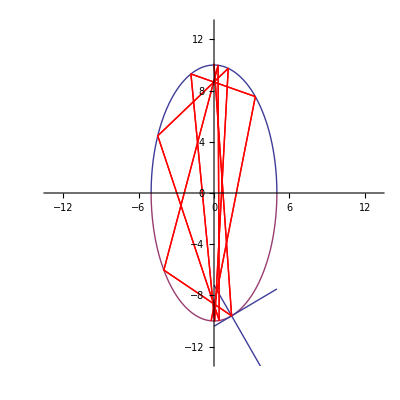

```mathematica
(* Picture confirming that we did this correctly *)
(* LOOKS GOOD!! *)
plpts = 11;
plpt =Take[pt,{1,plpts}];
g1=Plot[{Elow[x],Ehigh[x]},{x,-5,5},PlotRange->{{-13,13},{-13,13}},AspectRatio->1];
g2=Plot[tpln[pt[[2,1]],pt[[2,2]],x],{x,0,5}];
g3=Plot[pln[pt[[2,1]],pt[[2,2]],x],{x,0,5}];
g4 = ListLinePlot[plpt,PlotStyle->Red];
g5=Plot[lne,{x,-5,3},PlotStyle->Red];
g6=ListLinePlot[plpt,PlotStyle->Red];
Show[g1,g2,g3,g4,g6]
```